27.1226

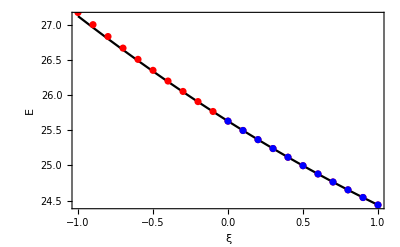

```mathematica
energyxit5={{1.,24.438223},{0.9,24.544414227188543},{0.8,24.653269464671986},{0.7,24.76484800399961},{0.6,24.879264921634583},{0.5,24.996611663749057},{0.4,25.116951309689714},{0.3,25.24040797095965},{0.2,25.36708284439682},{0.1,25.497040146657298},{0.,25.630417402000106}};
energyfull={{1.,24.438223},{0.9,24.544414227188543},{0.8,24.653269464671986},{0.7,24.76484800399961},{0.6,24.879264921634583},{0.5,24.996611663749057},{0.4,25.116951309689714},{0.3,25.24040797095965},{0.2,25.36708284439682},{0.1,25.497040146657298},{0.,25.630417402000106},{-0.1,25.767279809326244},{-0.2,25.90777049390361},{-0.3,26.051992339023208},{-0.4,26.200017612931532},{-0.5,26.35198778581875},{-0.6,26.508009591392405},{-0.7,26.668145127456405},{-0.8,26.832536475148622},{-0.9,27.001235331561553},{-1.,27.17437944484389}};
fit=Fit[energyxit5,{1,x,x^2},x];
fit//.x->-1
Show[Plot[fit,{x,-1,1},PlotStyle->Black],ListPlot[{energyfull,energyxit5},PlotStyle->{Red,Blue},PlotRange->{{0,1},{12,30}}],Frame->True,FrameLabel->{{HoldForm["E"],None},{HoldForm[ξ],None}},PlotLabel->None,LabelStyle->{10,GrayLevel[0]}]
```